### Book keeping

```mathematica
SetAttributes[print,HoldFirst]
```

```mathematica
print[variable_]:=Print[HoldForm[variable], " is ", variable]
```

### Fundamental group functions

```mathematica
findNextEdge[edge_,pairing_]:=Module[{firstVertex=edge[[2,1]],secondVertex=edge[[2,2]],nextEdge},
If[edge[[1]]≠pairing[[1,1]],Return["Edge is not in first tetrahedron"]];
If[Count[pairing[[1,2]],firstVertex]==0||Count[pairing[[1,2]],firstVertex]==0,Return["False"]];
nextEdge={pairing[[2,1]],{pairing[[2,2,(Position[pairing[[1,2]],firstVertex])[[1,1]]]],pairing[[2,2,(Position[pairing[[1,2]],secondVertex])[[1,1]]]]}};
Return[nextEdge];]
```

```mathematica
positionOfEdge[edgeVertices_]:=Complement[{1,2,3,4},{edgeVertices[[1]],edgeVertices[[2]]}];
```

```mathematica
isEdgeThere[allEdges_,edge_]:=If[Count[allEdges,edge]!=0||Count[allEdges,{edge[[1]],Reverse[edge[[2]]]}]≠0,Return[True],Return[False]];
```

```mathematica
edgeGluings[snapPeaData_]:=
(*Takes input in form = [tet1, ...tetn], tet = [face1,...face4], 
face = [this tet face,next tet face], this tet face = {tet number, vertices} *)
Module[{numOfTet=Length[snapPeaData],edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},allEdges,startingEdge,currentEdge,currentTet,end1=1,end=1,gluings,finalGluings={},j=1,i=1,edgeCount=0},
(*Pick an edge. Follow it around. Stop when you get back where you started. Store edge gluings*)
(*Edges will have format: {tet,{edgepair}}*)
allEdges=Flatten[Table[{i,edge},{i,numOfTet},{edge,edges}],1];

While[end1≠0&&Length[allEdges]≠0, (*for each edge in the quotient manifold*)
currentEdge=allEdges[[1]];
startingEdge=currentEdge;
gluings={};
i=1;
end=1;
While[end≠0,(*For each face pairing*)
i=i+1;
allEdges=Complement[allEdges,{currentEdge,{currentEdge[[1]],Reverse[currentEdge[[2]]]}}];(*Remove current edge from all edges*)
currentTet=currentEdge[[1]];
edgeVertices=currentEdge[[2]];
(*Print[currentTet]; 
Print[currentEdge];
Print[snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[1]]]]];
Print[snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[2]]]]];*)
nextEdges=Table[findNextEdge[currentEdge,snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[i]]]]],{i,2}];
If[isEdgeThere[allEdges,nextEdges[[1]]]==True, (*If nextEdges[1] hasn't been used*)
currentEdge=nextEdges[[1]];
gluings=Join[gluings,{snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[1]]]]}];,
If[isEdgeThere[allEdges,nextEdges[[2]]]==True, (* if not true, if nextEdge[2] hasn't been used*) 
currentEdge=nextEdges[[2]]; 
gluings=Join[gluings,{snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[2]]]]}];, (*If false must have completed holonomy around current edge*)
If[nextEdges[[1]]==startingEdge, (*If nextEdge[1] is starting edge*)gluings=Join[gluings,{snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[1]]]]}],
(*If nextEdge[2] is starting edge*)gluings=Join[gluings,{snapPeaData[[currentTet,(positionOfEdge[edgeVertices])[[2]]]]}]]; (*ends finished holonomy If*)
allEdges=Complement[allEdges,{currentEdge,{currentEdge[[1]],Reverse[currentEdge[[2]]]}}];
end=0](*end = 0 is only holonomy has completed.*)
]; (*end If 1*)
]; (*end While 2*)
finalGluings=Join[finalGluings,{gluings}];
]; (*end While 1*)
Return[finalGluings];]
```

#### Convert from condensed snap Pea to Regina format

```mathematica
expandSnapPea[snapPeaData_]:=Module[{numOfTet=4,tet,face},
expandedSnapPea=Table[{{tet,Delete[{1,2,3,4},face]},snapPeaData[[tet,face]]},{tet,1,numOfTet},{face,1,4}];
Return[expandedSnapPea]]
```

```mathematica
indexFrom1[snapPeaFrom0_]:=Module[{numOfTet=snapPeaFrom0[[1]],temp=snapPeaFrom0},
Do[temp[[2,tet,face]]=temp[[2,tet,face]]+1,{face,1,4},{tet,1,numOfTet}];
Return[temp]]
```

```mathematica
removeFaceVertex[snapPeaFrom1_]:=
Module[{numOfTet=Length[snapPeaFrom1],temp=snapPeaFrom1,tet,face},
Do[temp[[tet,face,2]]=Delete[temp[[tet,face,2]],face],{tet,1,numOfTet},{face,1,4}];
Return[temp]]
```

Examples

```mathematica
fig8={{{{1,{2,3,4}},{2,{4,1,3}}},{{1,{1,3,4}},{2,{3,4,2}}},{{1,{1,2,4}},{2,{1,4,2}}},{{1,{1,2,3}},{2,{3,2,1}}}},{{{2,{2,3,4}},{1,{4,1,3}}},{{2,{1,3,4}},{1,{3,4,2}}},{{2,{1,2,4}},{1,{1,4,2}}},{{2,{1,2,3}},{1,{3,2,1}}}}};
```

```mathematica
Length[rManHolonomy]
```

0

```mathematica
Manipulate[fig8Holonomy[[edge,face]],{edge,{1,2}},{face,{1,2,3,4,5,6},ControlType->Manipulator}]
```

#### Find and label group generators

```mathematica
generators[snapPeaData_]:=Module[{generators},
graph=dualSkeleton[snapPeaData];
generators=generatorsOfGraph[graph];
Return[generators]]
```

```mathematica
dualSkeleton[snapPeaData_]:=Module[{edgeList,facePairingsList,numOfFaces},
facePairingsList=facePairings[snapPeaData];
edgeList=Table[directedEdge[facePairing],{facePairing,facePairingsList}];
Return[edgeList]]
```

```mathematica
labeledDualSkeleton[snapPeaData_]:=Module[{labeledEdgeList,numOfTet=Length[snapPeaData],facePairingsList,edges,labels},
facePairingsList=facePairings[snapPeaData];
edges=Table[directedEdge[facePairing],{facePairing,facePairingsList}];
labels=Table[ToString[facePairingLetterLabel[facePairing,snapPeaData]],{facePairing,facePairingsList}];
labeledEdgeList=Table[Join[edges[[index]],{labels[[index]]}],{index,Length[edges]}];
(*labeledEdgeList=Table[Labeled[directedEdge[facePairing],ToString[facePairingLetterLabel[facePairing,snapPeaData]]],{facePairing,facePairingsList}];*)
Return[labeledEdgeList]]
```

```mathematica
facePairingLetterLabel[facePairing_,snapPeaData_]:=Module[{label,facePairingsList,labels},
labels=faceLabels[snapPeaData];
If[Count[Keys[labels],facePairing]==1,label=labels[facePairing],label=labels[[facePairing]]];
Return[label]];
```

```mathematica
nextTet[snapPeaData_,tet_,face_]:=snapPeaData[[tet,face,2,1]]
```

```mathematica
facePairingLabel[facePairing_]:=Module[{tet1,face1,tet2,face2,labledPairing},
tet1=facePairing[[1,1]];
face1=Complement[{1,2,3,4},facePairing[[1,2]]][[1]];
tet2=facePairing[[2,1]];
face2=Complement[{1,2,3,4},facePairing[[2,2]]][[1]];
labledPairing={{tet1,face1},{tet2,face2}};
Return[labledPairing]]
```

```mathematica
edge[facePairing_]:=Module[{tet1,tet2,edge},
tet1=facePairing[[1,1]];
tet2=facePairing[[2,1]];
Return[{tet1,tet2}]]
```

```mathematica
directedEdge[facePairing_]:=Module[{tet1,tet2,directedEdge},
tet1=facePairing[[1,1]];
tet2=facePairing[[2,1]];
directedEdge={tet1->tet2};
Return[directedEdge]]
```

```mathematica
labelHolonomy[holonomy_]:=Module[{relators=holonomy,facePairingList,facePairing,letters,numberOfPairings },
facePairingList=facePairings[holonomy];
numberOfPairings=Max[Table[Length[holonomy[[edge]]],{edge,1,Length[[holonomy]]}]];
letters=Table["a"<>ToString[index],{index,1,numberOfPairings}];
Do[relators=searchAndReplace[relators,facePairingList[[index]],letters[[1]]];
relators=searchAndReplace[relators,reverseFaceGluing[facePairingList[[index]]],letters[[1]]^(-1)];
letters=Delete[letters,1];,{index,Length[facePairingList]}];
Return[relators]]
```

```mathematica
labelHolonomy[holonomy_,snapPeaData_]:=Module[{relators=holonomy,facePairingList ,labels,reverseGluing},
facePairingList=facePairings[snapPeaData];
labels=faceLabels[snapPeaData];
Do[relators=searchAndReplace[relators,facePairing,labels[facePairing]];reverseGluing=reverseFaceGluing[facePairing];
relators=searchAndReplace[relators,reverseGluing,labels[facePairing]^(-1)];
,{facePairing,facePairingList}];
Return[relators]]
```

```mathematica
faceLabels[snapPeaData_]:=Module[{faceLabels,labelsList,numOfFaces=Length[snapPeaData]*2,labels,facePairingsList},
labels=Table["a"<>ToString[index],{index,1,numOfFaces}];
facePairingsList=facePairings[snapPeaData];
faceLabels=AssociationThread[facePairingsList,labels];
Return[faceLabels]]
```

```mathematica
searchAndReplace[holonomy_,find_,replace_]:=Module[{modifiedHolonomy=holonomy,positionList,replacementList},
positionList=Position[modifiedHolonomy,find];
replacementList=positionListToReplacements[positionList,replace];
modifiedHolonomy=ReplacePart[modifiedHolonomy,replacementList];
Return[modifiedHolonomy]]
```

```mathematica
positionListToReplacements[positionList_,replace_]:=Module[{replacementList=positionList},
replacementList=Table[replacementList[[index]]->replace,{index,1,Length[positionList]}];
Return[replacementList]]
```

```mathematica
facePairings[holonomy_]:=Module[{numOfEdges=Length[holonomy],facePairing,facePairings={},edge},
Do[facePairing=holonomy[[edge,gluing]];
If[Count[facePairings,facePairing]==0&&Count[facePairings,reverseFaceGluing[facePairing]]==0,facePairings=Append[facePairings,facePairing]],{edge,1,numOfEdges},{gluing,1,Length[holonomy[[edge]]]}];
Return[facePairings]]
```

```mathematica
reverseFaceGluing[faceGluing_]:=Module[{tet1=faceGluing[[1,1]],tet2=faceGluing[[2,1]],reversedFaceGluing,faceVertex,orderedVertices2,matchedVertices1,vertex},
orderedVertices2=Sort[faceGluing[[2,2]]];
matchedVertices1=Flatten[Table[faceGluing[[1,2,Position[faceGluing[[2,2]],vertex][[1]]]],{vertex,orderedVertices2}]];
reversedFaceGluing={{tet2,orderedVertices2},{tet1,matchedVertices1}};
Return[reversedFaceGluing]]
```

#### Fundamental Group of the boundary

```mathematica
relators[boundaryTri_]:=Module[{relators},

Return[relators]]
```

```mathematica
directedEdge2[facePairing_]:=Module[{edge},
edge={facePairing[[1,1]]->facePairing[[2,1]]};
Return[edge]]
```

```mathematica
facePairings2[boundaryTri_]:=Module[{numOfTri=Length[boundaryTri],facePairing,facePairings={},tri},
Do[facePairing=boundaryTri[[tri,face]];
If[Count[facePairings,facePairing]==0&&Count[facePairings,reverseFaceGluing[facePairing]]==0,facePairings=Append[facePairings,facePairing]],{tri,1,numOfTri},{face,1,3}];
Return[facePairings]]
```

```mathematica
faceLabels2[boundaryTri_]:=Module[{faceLabels,labelsList,numOfFaces=Length[boundaryTri]*3/2,labels,facePairingsList},
labels=Table["a"<>ToString[index],{index,1,numOfFaces}];
facePairingsList=facePairings[boundaryTri];
faceLabels=AssociationThread[facePairingsList,labels];
Return[faceLabels]]
```

```mathematica
labeledDualSkeleton2[boundaryTri_,boundaryAssociation_]:=Module[{labeledEdgeList,numOfTet=Length[boundaryTri],facePairingsList,edges,labels},facePairingsList=facePairings[boundaryTri];
edges=Table[directedEdge2[facePairing],{facePairing,facePairingsList}];
labels=Table[ToString[boundaryAssociation[facePairing]],{facePairing,facePairingsList}];
labeledEdgeList=Table[Join[edges[[index]],{labels[[index]]}],{index,Length[edges]}];
Return[labeledEdgeList]]
```

```mathematica
labeledDualSkeleton2[faceLabels[
```

```mathematica
facePairingLetterLabel2[facePairing_,boundaryAssociation_]:=Module[{label,facePairingsList,labels},
labels=faceLabels2[boundaryTri];
If[Count[Keys[labels],facePairing]==1,label=labels[facePairing],label=labels[reverseFaceGluing[facePairing]]];
Return[label]];
```

```mathematica
face[snapPeaData_,tet_,vertex_,faceNumber_]:=Module[{face,nextTet,facePairing,currentEdges,nextVertex,positionOfVertex,positionOfEdges,nextEdges},
facePairing=snapPeaData[[tet,faceNumber]];
currentEdges=Complement[{1,2,3,4},{vertex,faceNumber}];
nextTet=facePairing[[2,1]];
positionOfVertex=Position[facePairing[[1,2]],vertex];
If[positionOfVertex=={},Print["face pairing and vertex"];Print[facePairing];Print[vertex]];
positionOfEdges=Table[Position[facePairing[[1,2]],currentEdges[[edge]]][[1,1]],{edge,1,2}];
nextVertex=facePairing[[2,2,positionOfVertex[[1,1]]]];
nextEdges=Table[facePairing[[2,2,position]],{position,positionOfEdges}];
face={{{tet,vertex},currentEdges},{{nextTet,nextVertex},nextEdges}};
Return[face]]
```

```mathematica
manTriToBoundaryTri[snapPeaData_]:=Module[{boundaryTri,numOfTet=Length[snapPeaData]},
(*takes 3-man tri and out puts boundary tri in formd
tri = {triangle1,...triangleN}, triangle = {face1,...face3}, face = {currentFace,nextFace}, nextFace = {nextTri,{gluing}}*)
boundaryTri=Flatten[Table[face[snapPeaData,tet,vertex,faceNumber],{tet,1,numOfTet},{vertex,1,4},{faceNumber,Complement[{1,2,3,4},{vertex}]}],1];
Return[boundaryTri]]
```

```mathematica
vertexGluings2[boundaryTri_]:=(*Takes input in form=[tet1,...tetn],tet=[face1,...face4],face=[this tet face,next tet face],this tet face={tet number,vertices}*)Module[{numOfTri=Length[boundaryTri],vertices={1,2,3},allVertices,startingVertex,currentVertex,currentTet,end1=1,end=1,gluings,finalGluings={},j=1,i=1,vertexCount=0,numOfTet=Length[boundaryTri]/4,currentVertexVertices,nextVerticesList,nextPairingsList},(*Pick an vertex.Follow it around.Stop when you get back where you started.Store vertex gluings*)(*Vertices will have format:{tet,{vertexpair}}*)
allVertices=Flatten[Table[{{tet,tetVertex},vertex},{tet,1,numOfTet},{tetVertex,1,4},{vertex,Complement[{1,2,3,4},{tetVertex}]}],2];

While[end1≠0&&Length[allVertices]≠0&&j<20,(*for each vertex in the quotient manifold*)
currentVertex=allVertices[[1]];
startingVertex=currentVertex;
gluings={};

j=j+1;
i=1;
end=1;

While[end≠0&&i<27&&Length[allVertices]≠0,(*For each face pairing*)
i=i+1;
Print[currentVertex];
allVertices=Complement[allVertices,{currentVertex}];(*Remove current vertex from all vertices*)
nextPairingsList=nextPairings[boundaryTri,currentVertex];
nextVerticesList=nextVertices[boundaryTri,currentVertex];

If[Count[allVertices,nextVerticesList[[1]]]==1,(*If nextVertices[1] hasn't been used*)
currentVertex=nextVerticesList[[1]];
gluings=Append[gluings,nextPairingsList[[1]]],

If[Count[allVertices,nextVerticesList[[2]]]==1,(*if not true,if nextVertex[2] hasn't been used*)
currentVertex=nextVerticesList[[2]];
gluings=Append[gluings,nextPairingsList[[2]]],

If[nextVerticesList[[1]]==startingVertex,(*If nextVertex[1] is starting vertex*)
gluings=Append[gluings,nextPairingsList[[1]]];
end=0,
(*If nextVertex[2] is starting vertex*)

If[nextVerticesList[[2]]==startingVertex,
gluings=Append[gluings,nextPairingsList[[2]]];
end=0, Print["problem"]
]
] (*end If 3. end=0 is only holonomy has completed.*)
] (*end If 2*) 
](*end If 1*)
];(*end While 2*)
finalGluings=Join[finalGluings,{gluings}];];(*end While 1*)
Return[finalGluings];]
```

```mathematica
rManBoundaryHolonomy=vertexGluings2[rManBoundary];
```

```mathematica
Length[rManBoundaryHolonomy]
```

0

```mathematica
labelBoundaryHolonomy[faceLabels[rMan],rManBoundaryHolonomy]
```

labelBoundaryHolonomy[<||>,{}]

```mathematica
nextVertices[boundaryTri_,vertex_]:=Module[{nextVertices,validPairings,nextVertexPositions},
validPairings=nextPairings[boundaryTri,vertex];
nextVertexPositions=Table[Position[validPairings[[pairing,1,2]],vertex[[2]]][[1]],{pairing,1,2}];
nextVertices=Table[{validPairings[[pairing,2,1]],validPairings[[pairing,2,2,nextVertexPositions[[pairing]]]][[1]]},{pairing,1,2}];
Return[nextVertices]]
```

```mathematica
nextPairings[boundaryTri_,vertex_]:=Module[{validPairings,savePositions,currentTet,currentTetVertex,currentVertex,pairings},
currentTet=vertex[[1,1]];
currentTetVertex=vertex[[1,2]];
pairings=boundaryTri[[4*(currentTet-1)+currentTetVertex]];
savePositions=Table[If[Count[pairings[[pairing,1,2]],vertex[[2]]]==0,pairing,##&[]],{pairing,1,3}];
validPairings=Delete[pairings,savePositions[[1]]];
Return[validPairings]]
```

```mathematica
labelHolonomy2[tri_,boundaryTri_,holonomy_]:=Module[{faceLabelsAssociation,labeledHolonomy,labels},
labels=faceLabels2[boundaryTri];
faceLabelsAssociation=faceLabels[tri];
Return[labeledHolonomy]]
```

#### Examples

### Labeling boundary holonomy

```mathematica
manifoldAssociationToBoundaryAssociation[association_]:=Module[{currentBoundaryAssociations,allBoundaryAssociations=<||>,label,faces},
Do[ label=Table[association[key],{face,1,3}];
faces=manPairingToBoundaryPairings[key];
currentBoundaryAssociations=AssociationThread[faces,label];
allBoundaryAssociations=Join[allBoundaryAssociations,currentBoundaryAssociations],
{key,Keys[association]}];
Return[allBoundaryAssociations]]
```

```mathematica
manPairingToBoundaryPairings[pairing_]:=Module[{pairings,allowedVertices,tet,edges,pairedTet,face},
tet=pairing[[1,1]];
face=Complement[{1,2,3,4},pairing[[1,2]]];
allowedVertices=Complement[{1,2,3,4},face];
pairedTet=pairing[[2,1]];
pairings=Table[{{{tet,tetVertex},Sort[Complement[allowedVertices,{tetVertex}]]},{{pairedTet,pairedVertex[pairing,tetVertex]},pairedEdges[pairing,face[[1]],tetVertex]}},{tetVertex,allowedVertices}];
Return[pairings]]
```

```mathematica
manifoldAssociationToBoundaryAssociation[faceLabels[rMan]]
```

<||>

```mathematica
pairedVertex[pairing_,vertex_]:=Module[{returnVertex,positionOfVertex},
positionOfVertex=Position[pairing[[1,2]],vertex][[1,1]];
returnVertex=pairing[[2,2,positionOfVertex]];
Return[returnVertex]]
```

```mathematica
pairedEdges[pairing_,face_,vertex_]:=Module[{pairings,positions,vertices,edges},
vertices=Complement[{1,2,3,4},{face,vertex}];
positions=Table[Position[pairing[[1,2]],vertices[[index]]][[1,1]],{index,1,2}];
edges=Table[pairing[[2,2,positions[[index]]]],{index,1,2}];
Return[edges]]
```

```mathematica
labelBoundaryHolonomy[manifoldAssociation_,boundaryHolonomy_]:=Module[{labeledBoundaryHolonomy,boundaryAssociation,numOfVertices=Length[boundaryHolonomy]},
boundaryAssociation=manifoldAssociationToBoundaryAssociation[manifoldAssociation];
labeledBoundaryHolonomy=Table[ If[Count[Keys[boundaryAssociation],pairing]==1,boundaryAssociation[pairing],1/boundaryAssociation[reverseFaceGluing[pairing]]],{index,1,numOfVertices},{pairing,boundaryHolonomy[[index]]}];
Return[labeledBoundaryHolonomy]]
```

### Summary of functions

Example: fig8 
Manifold fundamental group
fig8Holonomy = edgeGluings[snapPeaData] gives gluings around each edge in snap pea format 
labeledFig8 = labelHolonomy[holonomy, snapPeaData] labels it 
labeledDualSkeleton[snapPeaData]  shows generators on dual skeleton

Boundary fundamental group

manTriToBoundaryTri[snapPeaData] gives boundary triangulation
vertexGluings2[boundaryTri] gives gluings around vertices 
labelBoundaryHolonomy[faceLabels[snapPeaData], boundaryHolonomy] gives labeled boundary relators
GraphPlot[labeledDualSkeleton2[boundaryTri ],EdgeLabeling→True] gives labeled generators

### Examples

#### Fig8

```mathematica
fig8={{{{1,{2,3,4}},{2,{4,1,3}}},{{1,{1,3,4}},{2,{3,4,2}}},{{1,{1,2,4}},{2,{1,4,2}}},{{1,{1,2,3}},{2,{3,2,1}}}},{{{2,{2,3,4}},{1,{4,1,3}}},{{2,{1,3,4}},{1,{3,4,2}}},{{2,{1,2,4}},{1,{1,4,2}}},{{2,{1,2,3}},{1,{3,2,1}}}}};
```

```mathematica
fig8Holonomy=edgeGluings[fig8];
```

```mathematica
labeledFig8=labelHolonomy[fig8Holonomy,fig8]
```

{{a3,1/a1,a4,1/a3,a2,1/a4},{a2,1/a1,a3,1/a2,a1,1/a4}}

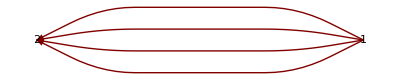

```mathematica
GraphPlot[labeledDualSkeleton[fig8],EdgeLabeling->True,VertexLabeling->True,DirectedEdges->True]
```

```mathematica
fig8Boundary=manTriToBoundaryTri[fig8];
```

```mathematica
fig8BoundaryHolonomy=vertexGluings2[fig8Boundary];
```

{{1,1},2}

{{2,1},4}

{{1,3},2}

{{2,1},2}

{{1,1},4}

{{2,3},2}

{{1,1},3}

{{2,3},4}

{{1,4},2}

{{2,2},4}

{{1,4},3}

{{2,3},1}

{{1,2},1}

{{2,4},1}

{{1,2},3}

{{2,2},1}

{{1,4},1}

{{2,2},3}

{{1,2},4}

{{2,4},3}

{{1,3},1}

{{2,1},3}

{{1,3},4}

{{2,4},2}

```mathematica
fig8BoundaryLabels=manifoldAssociationToBoundaryAssociation[faceLabels[fig8]];
```

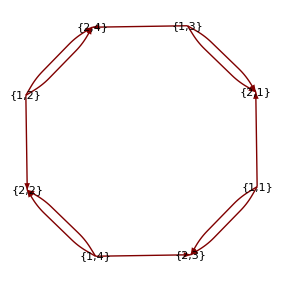

```mathematica
GraphPlot[labeledDualSkeleton2[fig8Boundary,fig8BoundaryLabels],EdgeLabeling->True,VertexLabeling->True,DirectedEdges->True]
```

```mathematica
labelBoundaryHolonomy[faceLabels[fig8],fig8BoundaryHolonomy]
```

{{a3,1/a1,a4,1/a3,a2,1/a4},{a2,1/a1,a3,1/a2,a1,1/a4},{a3,1/a1,a4,1/a3,a2,1/a4},{a1,1/a2,a4,1/a1,a2,1/a3}}

#### Regina manifold

```mathematica
unsimplifiedRManifold={4,{{{1,{0,3,2,1}},{1,{2,1,0,3}},{1,{3,1,2,0}},{2,{1,2,3,0}}},{{0,{0,3,2,1}},{0,{2,1,0,3}},{0,{3,1,2,0}},{3,{2,3,1,0}}},{{0,{3,0,1,2}},{3,{2,1,0,3}},{3,{2,0,3,1}},{3,{3,0,1,2}}},{{1,{3,2,0,1}},{2,{2,1,0,3}},{2,{1,2,3,0}},{2,{1,3,0,2}}}}};
```

```mathematica
rManFrom0 = unsimplifiedRManifold[[2]];
```

```mathematica
rManFrom1=rManFrom0+1;
```

```mathematica
removedFaceVertex= removeFaceVertex[rManFrom1];
```

```mathematica
rMan=expandSnapPea[removedFaceVertex];
```

```mathematica
rManHolonomy=edgeGluings[expandedSnapPea];
```

```mathematica
labeledRManHolonomy=labelHolonomy[rManHolonomy,rMan]
```

{{a3,1/a1,a3,a5,1/a6,a7,1/a5,1/a2,a4,a7,1/a8,1/a4},{a2,1/a1,a4,a6,1/a8,a7,1/a6,a8,1/a5,1/a1,a2,1/a3}}

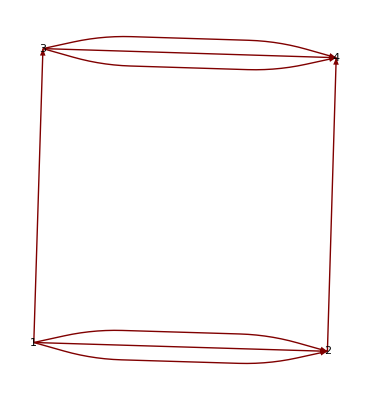

```mathematica
GraphPlot[labeledDualSkeleton[rMan],EdgeLabeling->True,VertexLabeling->True,DirectedEdges->True]
```

```mathematica
rManBoundary=manTriToBoundaryTri[rMan];
```

```mathematica
rManBoundaryHolonomy=vertexGluings2[rManBoundary];
```

{{1,1},2}

{{2,4},2}

{{1,2},4}

{{2,2},1}

{{4,4},3}

{{3,4},1}

{{4,2},3}

{{2,3},1}

{{1,1},3}

{{3,2},4}

{{4,1},2}

{{3,2},3}

{{1,1},4}

{{2,3},4}

{{1,3},2}

{{3,4},3}

{{4,4},1}

{{3,1},2}

{{4,3},1}

{{3,1},3}

{{4,4},2}

{{2,2},3}

{{1,4},3}

{{2,4},1}

{{1,2},1}

{{2,2},4}

{{1,4},2}

{{2,1},2}

{{4,3},4}

{{3,1},4}

{{4,3},2}

{{2,1},3}

{{1,3},1}

{{3,4},2}

{{4,2},1}

{{3,3},2}

{{1,2},3}

{{2,4},3}

{{1,4},1}

{{2,1},4}

{{1,3},4}

{{2,3},2}

{{4,2},4}

{{3,3},1}

{{4,1},3}

{{3,2},1}

{{4,1},4}

{{3,3},4}

```mathematica
boundaryLabels=manifoldAssociationToBoundaryAssociation[faceLabels[rMan]];
```

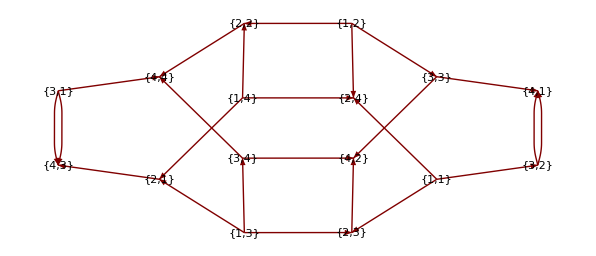

```mathematica
GraphPlot[labeledDualSkeleton2[rManBoundary,boundaryLabels],EdgeLabeling->True,VertexLabeling->True,DirectedEdges->True]
```

```mathematica
labelBoundaryHolonomy[faceLabels[rMan],rManBoundaryHolonomy]
```

{{a3,1/a1,a3,a5,1/a6,a7,1/a5,1/a2,a4,a7,1/a8,1/a4},{a2,1/a1,a4,a6,1/a8,a7,1/a6,a8,1/a5,1/a1,a2,1/a3},{a3,1/a1,a3,a5,1/a6,a7,1/a5,1/a2,a4,a7,1/a8,1/a4},{a1,1/a2,a3,1/a2,a1,a5,1/a8,a6,1/a7,a8,1/a6,1/a4}}

```mathematica
Dimensions[%]
```

{4,12}

### 2 manifold examples

```mathematica
face1={{{1,1},{2,3}},{{2,2},{1,2}}};
face2={{{1,1}{1,3}},{{2,2},{1,3}}};
face3={{{1,1},{1,2}},{{2,2},{2,3}}};
tri1={face1,face2,face3};
face21={{{2,2},{2,3}},{{1,1},{1,2}}};
face22={{{2,2},{1,3}},{{1,1},{1,3}}};
face23={{{2,2},{1,2}},{{1,1},{2,3}}};
tri2={face21,face22,face23};
torus={tri1,tri2};
```